```mathematica
<<"MaTeX`"
tex[x_,fontsize_]:=MaTeX[x,FontSize->fontsize];

tf[n1_,n2_,x1_,x2_,k1_,k2_,f_,b_,s_,w_,if_]:=MapThread[Prepend,{Flatten[Riffle[{{#,{-if,-1}1/(5w)}}&/@MaTeX[NumberForm[#,{f,b}]&/@#[1,{x1,x2}],FontSize->s],{Table[{Null,{-if,-1}1/(8w)},k2-1]},2],1],#[k2,{n1,n2}]}]&[Rescale[Subdivide[n1,n2,#1 k1],{n1,n2},#2]&];
tf[n1_,n2_,k1_,k2_,s_,w_,if_]:=tf[n1,n2,n1,n2,k1,k2,1,1,s,w,if];
tf[n1_,n2_,k1_,k2_,s_,w_]:=tf[n1,n2,n1,n2,k1,k2,1,1,s,w,0];
```

### Variation of Slater Orbital Overlap

```mathematica
orbs = {{1,62000},{2,46000},{3,38000},{4,33000},{5,30000},{6,27500},{7,26000},{8,24000},{10,22000}};
free[k_]:= 1.54 10^5/(2 k +1);
huck[k_]:= 4 β Sin[π/(4 k +2)];
```

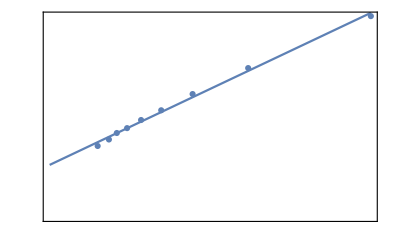

```mathematica
kval = {1,2,3,4,5,6,7,8,10};
huck[kval]/(4β) ;
nuOrbs = Transpose[orbs][[2]];
d1 = Transpose[{huck[kval]/(β),nuOrbs}];
d2 = Transpose[{free[kval]/(1.54 *10^5),nuOrbs}];
p1a = ListPlot[
d1,
PlotMarkers-> Automatic,
Joined-> False];
p2a = ListPlot[
d2,
PlotMarkers-> Automatic,
Joined-> False];

f1 =Fit[d1,{1,x},x];
a1 = f1/.x-> 0;
b1 = D[f1,x];
huckfit = Transpose[{kval,a1 +huck[kval]/.β-> b1}];
f2 =Fit[d2,{1,x},x];
a2 = f2/.x-> 0;
b2 = D[f2,x];

p1b = Plot[f1,{x,0,2}];
p2b = Plot[f2,{x,0,1.5}];
Show[p1a,p1b,FrameLabel-> {tex["\\sin(\\frac{\\pi}{4k+1})",16],tex["\\nu_\\text{orbs}",16]},
FrameTicks->{{tf[0,60000,4,5,10.5*100/72,10],None},{tf[0,2,4,5,10.5*100/72,10],None}},
Frame->True,
ImageSize->10*100/2.54,
FrameStyle->Directive[Black,AbsoluteThickness[1]]
]
linfit = Transpose[{kval,b2/(2 kval +1)+a2}];
```

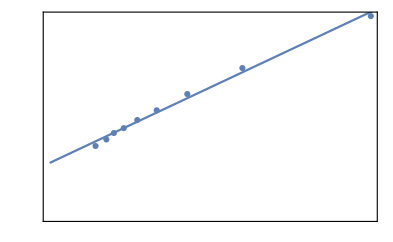

```mathematica
Show[p2a,p2b,
FrameLabel-> {MaTeX["\\frac{\\pi}{4k+1}"],MaTeX["\\nu_\\text{orbs}"]},
FrameTicks->{{tf[0,60000,4,5,10.5*100/72,10],None},{tf[0,0.4,4,5,10.5*100/72,10],None}},
Frame->True,
ImageSize->10*100/2.54,
FrameStyle->Directive[Black,AbsoluteThickness[1]]
]
```

```mathematica
data =Transpose[ {kval,free[kval],a1 +huck[kval]/.β->b1 ,nuOrbs}];
TableForm[data]
```

1 | 51333.3 | 63009.7 | 62000
2 | 30800. | 45119.1 | 46000
3 | 22000. | 37016.5 | 38000
4 | 17111.1 | 32438.3 | 33000
5 | 14000. | 29503.1 | 30000
6 | 11846.2 | 27463. | 27500
7 | 10266.7 | 25963.4 | 26000
8 | 9058.82 | 24814.9 | 24000
10 | 7333.33 | 23172. | 22000

```mathematica
TableForm[orbs]
```

1 | 62000
2 | 46000
3 | 38000
4 | 33000
5 | 30000
6 | 27500
7 | 26000
8 | 24000
10 | 22000

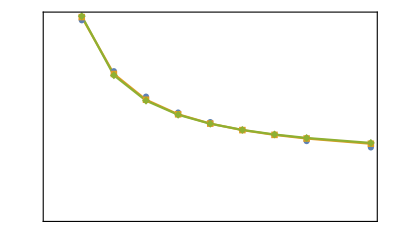

```mathematica
p1 = ListPlot[{orbs,huckfit,linfit},Joined-> {False,True,True},PlotMarkers-> {Automatic},PlotLegends->{tex["\\text{orbs}",20],tex["\\text{H\\\"uckel fit}",20],tex["\\text{line fit}",20]},
FrameLabel-> {tex["k",20],tex["\\nu_\\text{orbs}",20]},
FrameTicks->{{tf[0,60000,4,5,10.5*100/72,10],None},{tf[0,10,4,5,10.5*100/72,10],None}},
Frame->True,
ImageSize->10*100/2.54,
FrameStyle->Directive[Black,AbsoluteThickness[1]]]
```

```mathematica
slaterOrb[r_]:= Exp[-p](1 + p + 2 p^2/5  + p^3/15)/.{p-> 1.626 r/0.52}
guess = Series[slaterOrb[r],{r,1.39,1}]//Normal
```

0.238038-0.409956 (-1.39+r)

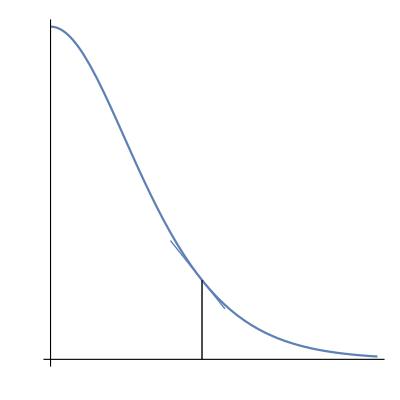

```mathematica
p1 =Plot[slaterOrb[r],{r,0,3},
AspectRatio-> 1,
AxesLabel-> {tex["R(\\text{A})",20],tex["S(2p\\pi,2p\\pi)",20]},
Ticks->{tf[0,3.0,4,5,10.5*100/72,10],tf[0,1.0,4,5,10.5*100/72,10]},
LabelStyle-> 16];
p2 = Plot[guess,{r,1.1,1.6},PlotStyle-> Thick];
Show[p1,p2,
Epilog-> {Line[{{1.39,slaterOrb[1.39]},{1.39,0}}]}]
```